```mathematica
ClearAll["Global`*"]
```

```mathematica
referenceChebyshev[n_] := Sum[ MangoldtLambda[ j],{j,2,n}]
L2[n_, 1,b_] := L2[n,1,b]=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
L2[n_, k_,b_ ]:= Sum[ L2[ n/j,k-1,b],{j,2,n}]-b Sum[ L2[ n/(j b),k-1,b],{j,1,n}]
ChebAlt[n_,b_]:=Sum[ (-1)^(a-1) L2[n,a,b] ,{a,1,Log[If[ b<2,b,2],n]}]+Sum[ b^a Log[b],{a,1,Log[b,n]}]
Table[ { n, N[referenceChebyshev[ n ]], N[ChebAlt[n,3/2]],N[ChebAlt[n,2]], N[ChebAlt[n,5]]},{n,2,100}]//TableForm
```

2 | 0.693147 | 0.693147 | 0.693147 | 0.693147
3 | 1.79176 | 1.79176 | 1.79176 | 1.79176
4 | 2.48491 | 2.48491 | 2.48491 | 2.48491
5 | 4.09434 | 4.09434 | 4.09434 | 4.09434
6 | 4.09434 | 4.09434 | 4.09434 | 4.09434
7 | 6.04025 | 6.04025 | 6.04025 | 6.04025
8 | 6.7334 | 6.7334 | 6.7334 | 6.7334
9 | 7.83201 | 7.83201 | 7.83201 | 7.83201
10 | 7.83201 | 7.83201 | 7.83201 | 7.83201
11 | 10.2299 | 10.2299 | 10.2299 | 10.2299
12 | 10.2299 | 10.2299 | 10.2299 | 10.2299
13 | 12.7949 | 12.7949 | 12.7949 | 12.7949
14 | 12.7949 | 12.7949 | 12.7949 | 12.7949
15 | 12.7949 | 12.7949 | 12.7949 | 12.7949
16 | 13.488 | 13.488 | 13.488 | 13.488
17 | 16.3212 | 16.3212 | 16.3212 | 16.3212
18 | 16.3212 | 16.3212 | 16.3212 | 16.3212
19 | 19.2657 | 19.2657 | 19.2657 | 19.2657
20 | 19.2657 | 19.2657 | 19.2657 | 19.2657
21 | 19.2657 | 19.2657 | 19.2657 | 19.2657
22 | 19.2657 | 19.2657 | 19.2657 | 19.2657
23 | 22.4012 | 22.4012 | 22.4012 | 22.4012
24 | 22.4012 | 22.4012 | 22.4012 | 22.4012
25 | 24.0106 | 24.0106 | 24.0106 | 24.0106
26 | 24.0106 | 24.0106 | 24.0106 | 24.0106
27 | 25.1092 | 25.1092 | 25.1092 | 25.1092
28 | 25.1092 | 25.1092 | 25.1092 | 25.1092
29 | 28.4765 | 28.4765 | 28.4765 | 28.4765
30 | 28.4765 | 28.4765 | 28.4765 | 28.4765
31 | 31.9105 | 31.9105 | 31.9105 | 31.9105
32 | 32.6036 | 32.6036 | 32.6036 | 32.6036
33 | 32.6036 | 32.6036 | 32.6036 | 32.6036
34 | 32.6036 | 32.6036 | 32.6036 | 32.6036
35 | 32.6036 | 32.6036 | 32.6036 | 32.6036
36 | 32.6036 | 32.6036 | 32.6036 | 32.6036
37 | 36.2146 | 36.2146 | 36.2146 | 36.2146
38 | 36.2146 | 36.2146 | 36.2146 | 36.2146
39 | 36.2146 | 36.2146 | 36.2146 | 36.2146
40 | 36.2146 | 36.2146 | 36.2146 | 36.2146
41 | 39.9281 | 39.9281 | 39.9281 | 39.9281
42 | 39.9281 | 39.9281 | 39.9281 | 39.9281
43 | 43.6893 | 43.6893 | 43.6893 | 43.6893
44 | 43.6893 | 43.6893 | 43.6893 | 43.6893
45 | 43.6893 | 43.6893 | 43.6893 | 43.6893
46 | 43.6893 | 43.6893 | 43.6893 | 43.6893
47 | 47.5395 | 47.5395 | 47.5395 | 47.5395
48 | 47.5395 | 47.5395 | 47.5395 | 47.5395
49 | 49.4854 | 49.4854 | 49.4854 | 49.4854
50 | 49.4854 | 49.4854 | 49.4854 | 49.4854
51 | 49.4854 | 49.4854 | 49.4854 | 49.4854
52 | 49.4854 | 49.4854 | 49.4854 | 49.4854
53 | 53.4557 | 53.4557 | 53.4557 | 53.4557
54 | 53.4557 | 53.4557 | 53.4557 | 53.4557
55 | 53.4557 | 53.4557 | 53.4557 | 53.4557
56 | 53.4557 | 53.4557 | 53.4557 | 53.4557
57 | 53.4557 | 53.4557 | 53.4557 | 53.4557
58 | 53.4557 | 53.4557 | 53.4557 | 53.4557
59 | 57.5332 | 57.5332 | 57.5332 | 57.5332
60 | 57.5332 | 57.5332 | 57.5332 | 57.5332
61 | 61.6441 | 61.6441 | 61.6441 | 61.6441
62 | 61.6441 | 61.6441 | 61.6441 | 61.6441
63 | 61.6441 | 61.6441 | 61.6441 | 61.6441
64 | 62.3372 | 62.3372 | 62.3372 | 62.3372
65 | 62.3372 | 62.3372 | 62.3372 | 62.3372
66 | 62.3372 | 62.3372 | 62.3372 | 62.3372
67 | 66.5419 | 66.5419 | 66.5419 | 66.5419
68 | 66.5419 | 66.5419 | 66.5419 | 66.5419
69 | 66.5419 | 66.5419 | 66.5419 | 66.5419
70 | 66.5419 | 66.5419 | 66.5419 | 66.5419
71 | 70.8046 | 70.8046 | 70.8046 | 70.8046
72 | 70.8046 | 70.8046 | 70.8046 | 70.8046
73 | 75.0951 | 75.0951 | 75.0951 | 75.0951
74 | 75.0951 | 75.0951 | 75.0951 | 75.0951
75 | 75.0951 | 75.0951 | 75.0951 | 75.0951
76 | 75.0951 | 75.0951 | 75.0951 | 75.0951
77 | 75.0951 | 75.0951 | 75.0951 | 75.0951
78 | 75.0951 | 75.0951 | 75.0951 | 75.0951
79 | 79.4645 | 79.4645 | 79.4645 | 79.4645
80 | 79.4645 | 79.4645 | 79.4645 | 79.4645
81 | 80.5631 | 80.5631 | 80.5631 | 80.5631
82 | 80.5631 | 80.5631 | 80.5631 | 80.5631
83 | 84.982 | 84.982 | 84.982 | 84.982
84 | 84.982 | 84.982 | 84.982 | 84.982
85 | 84.982 | 84.982 | 84.982 | 84.982
86 | 84.982 | 84.982 | 84.982 | 84.982
87 | 84.982 | 84.982 | 84.982 | 84.982
88 | 84.982 | 84.982 | 84.982 | 84.982
89 | 89.4706 | 89.4706 | 89.4706 | 89.4706
90 | 89.4706 | 89.4706 | 89.4706 | 89.4706
91 | 89.4706 | 89.4706 | 89.4706 | 89.4706
92 | 89.4706 | 89.4706 | 89.4706 | 89.4706
93 | 89.4706 | 89.4706 | 89.4706 | 89.4706
94 | 89.4706 | 89.4706 | 89.4706 | 89.4706
95 | 89.4706 | 89.4706 | 89.4706 | 89.4706
96 | 89.4706 | 89.4706 | 89.4706 | 89.4706
97 | 94.0453 | 94.0453 | 94.0453 | 94.0453
98 | 94.0453 | 94.0453 | 94.0453 | 94.0453
99 | 94.0453 | 94.0453 | 94.0453 | 94.0453
100 | 94.0453 | 94.0453 | 94.0453 | 94.0453

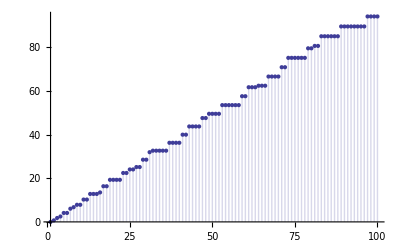

```mathematica
DiscretePlot[ChebAlt[ n,  3/2],{n,1,100}]
```

```mathematica
referenceChebyshev[n_] := Sum[ MangoldtLambda[ j],{j,2,n}]
```

```mathematica
DiscretePlot[ referenceChebyshev[ n ],{n,1,100}]
```

-Graphics-

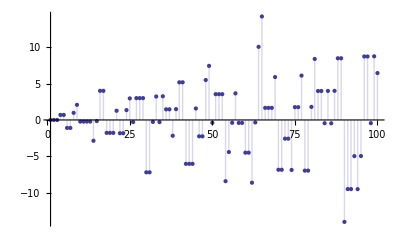

```mathematica
DiscretePlot[ L2[ n, 2, 2],{n,1,100}]
```

```mathematica
Expand[L2[10,1,2]]
```

-Log[2]+Log[3]-Log[4]+Log[5]-Log[6]+Log[7]-Log[8]+Log[9]-Log[10]

```mathematica
Sum[ (-1)^(j+1)/j,{j,1,Infinity}]
```

Log[2]